# q q̄→μ μ in EW theory (SM ): UV divergences

```mathematica
CKM = IndexDelta;
Neglect[MU] = Neglect[MU2] = 0;
Neglect[MM] = Neglect[MM2] = 0;

process ={-F[3, {1}], F[3, {1}]} -> {-F[2, {2}], F[2, {2}]} ;

SetOptions[InsertFields,  Model -> "SM",InsertionLevel->{Particles}, Restrictions -> NoLightFHCoupling];
SetOptions[CalcFeynAmp,PaVeReduce->True];
```

```mathematica
MASSES={MU->0,MU2->0,MM->0,MM2->0,S+T+U->0}
```

{MU→0,MU2→0,MM→0,MM2→0,S+T+U→0}

## Feynman Diagrams

## Tree Level

loading generic model file /home/arianna/Documenti/FeynArts-3.11/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /home/arianna/Documenti/FeynArts-3.11/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counterterms of order 1

> 6 counterterms of order 2

classes model {SM} initialized

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

Restoring 18 field point(s)

in total: 2 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams



FeynArtsGraphics[][([1] | [2])]

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

in total: 2 Particles amplitudes

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-amp-1.frm

running FORM...

ok

```mathematica
tops = CreateTopologies[0, 2 -> 2];
ins = InsertFields[tops, process];
Paint[ins,ColumnsXRows->{2,1},Numbering->Simple,
SheetHeader->None,ImageSize->{512,256}]
born1=CreateFeynAmp[ins];
born = CalcFeynAmp[born1];
```

## Self Energies

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 10 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 65 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

Restoring 18 field point(s)

in total: 75 Particles insertions

> Top. 1 aebe/cfdf/egfggg.m, 0 diagrams

> Top. 2 aebe/cfdf/egfhghgh.m, 0 diagrams

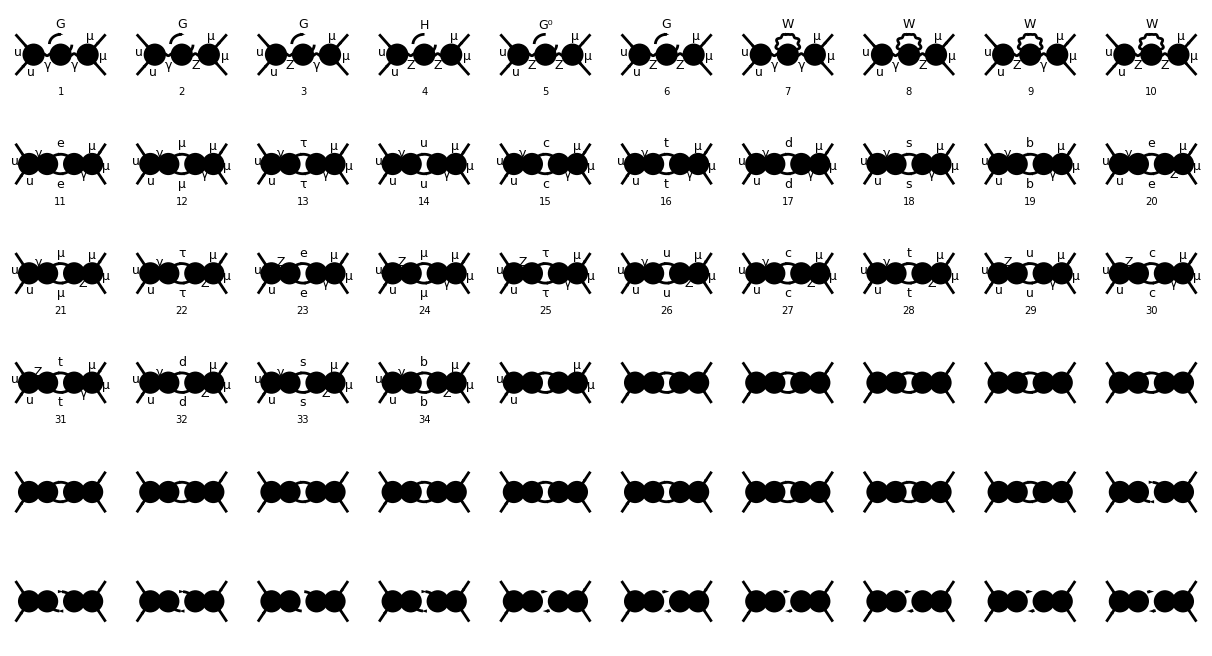

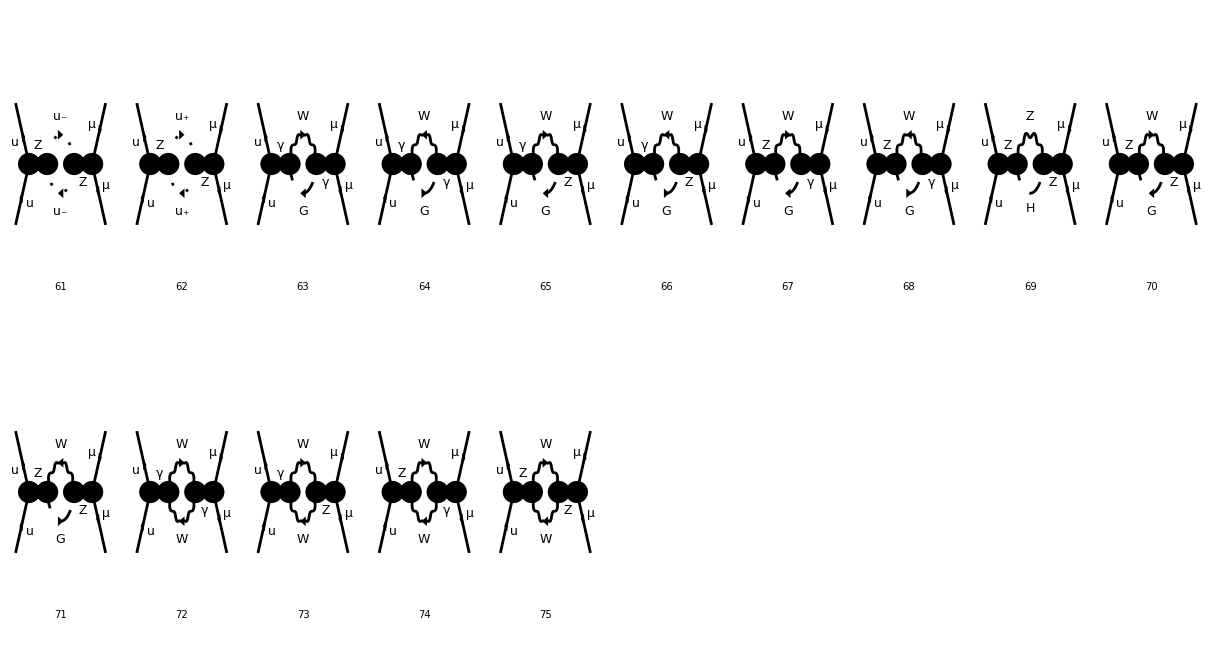

FeynArtsGraphics[][([1] | [2] | [3] | [4] | [5] | [6] | [7] | [8] | [9] | [10]
[11] | [12] | [13] | [14] | [15] | [16] | [17] | [18] | [19] | [20]
[21] | [22] | [23] | [24] | [25] | [26] | [27] | [28] | [29] | [30]
[31] | [32] | [33] | [34] | [35] | [36] | [37] | [38] | [39] | [40]
[41] | [42] | [43] | [44] | [45] | [46] | [47] | [48] | [49] | [50]
[51] | [52] | [53] | [54] | [55] | [56] | [57] | [58] | [59] | [60]),([61] | [62] | [63] | [64] | [65] | [66] | [67] | [68] | [69] | [70]
[71] | [72] | [73] | [74] | [75] | Null | Null | Null | Null | Null
Null | Null | Null | Null | Null | Null | Null | Null | Null | Null
Null | Null | Null | Null | Null | Null | Null | Null | Null | Null
Null | Null | Null | Null | Null | Null | Null | Null | Null | Null
Null | Null | Null | Null | Null | Null | Null | Null | Null | Null)]

creating amplitudes at level(s) {Particles}

> Top. 1: 10 Particles amplitudes

> Top. 2: 65 Particles amplitudes

in total: 75 Particles amplitudes

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-amp-1.frm

running FORM...

ok

```mathematica
tops2 = CreateTopologies[1, 2 -> 2, SelfEnergiesOnly];
ins2 = InsertFields[tops2, process];
ins2 = DiagramSelect[ins2, FreeQ[#, Field[5|6] -> S]&];
Paint[ins2,ColumnsXRows->{10,6},Numbering->Simple,
SheetHeader->None,ImageSize->{1212,656}]
selfff=CreateFeynAmp[ins2];
self = CalcFeynAmp[selfff];
```

```mathematica
selfdiv= UVDivergentPart[self[[1]]];
provaself = Unabbr[SSSSS*selfdiv] ;
```

## Vertices

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 7 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 8 Particles insertions

> Top. 7: 0 Particles insertions

> Top. 8: 0 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

> Top. 13: 0 Particles insertions

> Top. 14: 0 Particles insertions

> Top. 15: 0 Particles insertions

> Top. 16: 0 Particles insertions

> Top. 17: 0 Particles insertions

> Top. 18: 0 Particles insertions

> Top. 19: 0 Particles insertions

> Top. 20: 0 Particles insertions

> Top. 21: 0 Particles insertions

> Top. 22: 0 Particles insertions

> Top. 23: 0 Particles insertions

> Top. 24: 0 Particles insertions

Restoring 18 field point(s)

in total: 15 Particles insertions

> Top. 1 aebe/cfdg/ehfgfhgh.m, 0 diagrams

> Top. 2 aebf/cgdg/ghefehfh.m, 0 diagrams

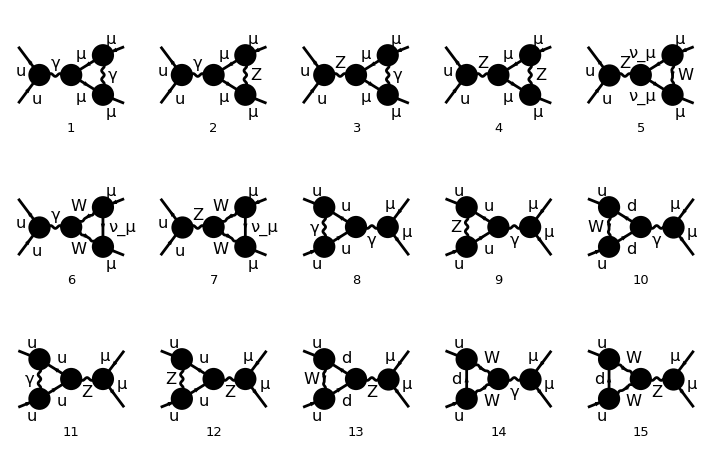

FeynArtsGraphics[][([1] | [2] | [3] | [4] | [5]
[6] | [7] | [8] | [9] | [10]
[11] | [12] | [13] | [14] | [15])]

creating amplitudes at level(s) {Particles}

> Top. 1: 7 Particles amplitudes

> Top. 2: 8 Particles amplitudes

in total: 15 Particles amplitudes

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-amp-1.frm

running FORM...

ok

```mathematica
tops4 = CreateTopologies[1, 2 -> 2, TrianglesOnly];
ins4 = InsertFields[tops4, process];
ins4 = DiagramSelect[ins4, FreeQ[#, Field[5] -> S]&];
Paint[ins4,ColumnsXRows->{5,3},Numbering->Simple,
SheetHeader->None,ImageSize->{712,456}]
verttt=CreateFeynAmp[ins4];
vert = CalcFeynAmp[verttt];
```

```mathematica
vertdiv = UVDivergentPart[vert[[1]]];
provavert = Unabbr[VVVVV *vertdiv] ;
```

## Boxes

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 4 Particles insertions

> Top. 8: 5 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

Restoring 18 field point(s)

in total: 9 Particles insertions

> Top. 1 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 2 aebf/cgdh/efehfggh.m, 0 diagrams

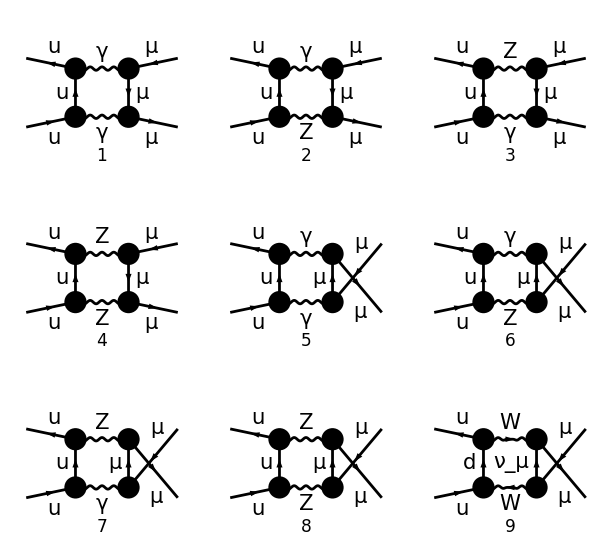

FeynArtsGraphics[][([1] | [2] | [3]
[4] | [5] | [6]
[7] | [8] | [9])]

creating amplitudes at level(s) {Particles}

> Top. 1: 4 Particles amplitudes

> Top. 2: 5 Particles amplitudes

in total: 9 Particles amplitudes

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-amp-1.frm

running FORM...

ok

```mathematica
tops5 = CreateTopologies[1, 2 -> 2, BoxesOnly];
ins5 = InsertFields[tops5, process];
Paint[ins5,ColumnsXRows->{3,3},Numbering->Simple,
SheetHeader->None,ImageSize->{612,556}]
box1=  CreateFeynAmp[ins5];
box = CalcFeynAmp[box1];
```

### UV divergent part Boxes:

NO UV divergent part in these diagrams.

```mathematica
bboxUV=UVDivergentPart[box[[1]]]/.{Divergence->1/ϵ} //Simplify
FreeQ[bboxUV,1/ϵ]
```

(Alfa2 (Sub542+Sub557/(CW2^2 S)+(64 Sub591)/S+16 Sub625+(2 (-Sub598+(36 (Sub543+Sub612+S Sub615 U-F10 F9 (S+U)))/(S SW2^2 U)+(Sub611+8 Sub617-(32 (MM2+MU2) Sub599)/(U (-2 (MM2+MU2)+T+U)))/CW2))/T) Mat[SUN1])/(36 ϵ)

False

```mathematica
Unabbr[bboxUV]//.MASSES //Simplify
```

-1/(18 CW2^2 S SW2^2 T (S+T) U (T+U) ϵ)Alfa2 (S+T+U) Mat[SUNT[Col1,Col2]] (64 SW2^4 (S (T-3 U)+T (T-2 U)) (T+U) ((v̇ 1|7|u̇ 4)) ((u2|6|v3))+(T+U) (S (3-10 SW2+8 SW2^2)^2 T+(3-10 SW2+8 SW2^2)^2 T (T-2 U)-3 S (12 CW2^2+(3-10 SW2+8 SW2^2)^2) U) ((v̇ 1|6|u̇ 4)) ((u2|7|v3))-64 S SW2^2 T U ((v̇ 1|7|v3)) ((u̇ 4|6|u2))+256 S SW2^3 T U ((v̇ 1|7|v3)) ((u̇ 4|6|u2))-256 S SW2^4 T U ((v̇ 1|7|v3)) ((u̇ 4|6|u2))-48 SW2^2 T^2 U ((v̇ 1|7|v3)) ((u̇ 4|6|u2))+192 SW2^3 T^2 U ((v̇ 1|7|v3)) ((u̇ 4|6|u2))-192 SW2^4 T^2 U ((v̇ 1|7|v3)) ((u̇ 4|6|u2))-64 S SW2^2 U^2 ((v̇ 1|7|v3)) ((u̇ 4|6|u2))+256 S SW2^3 U^2 ((v̇ 1|7|v3)) ((u̇ 4|6|u2))-256 S SW2^4 U^2 ((v̇ 1|7|v3)) ((u̇ 4|6|u2))-48 SW2^2 T U^2 ((v̇ 1|7|v3)) ((u̇ 4|6|u2))+192 SW2^3 T U^2 ((v̇ 1|7|v3)) ((u̇ 4|6|u2))-192 SW2^4 T U^2 ((v̇ 1|7|v3)) ((u̇ 4|6|u2))-144 S SW2^2 T U ((v̇ 1|6|v3)) ((u̇ 4|7|u2))+384 S SW2^3 T U ((v̇ 1|6|v3)) ((u̇ 4|7|u2))-256 S SW2^4 T U ((v̇ 1|6|v3)) ((u̇ 4|7|u2))-108 SW2^2 T^2 U ((v̇ 1|6|v3)) ((u̇ 4|7|u2))+288 SW2^3 T^2 U ((v̇ 1|6|v3)) ((u̇ 4|7|u2))-192 SW2^4 T^2 U ((v̇ 1|6|v3)) ((u̇ 4|7|u2))-144 S SW2^2 U^2 ((v̇ 1|6|v3)) ((u̇ 4|7|u2))+384 S SW2^3 U^2 ((v̇ 1|6|v3)) ((u̇ 4|7|u2))-256 S SW2^4 U^2 ((v̇ 1|6|v3)) ((u̇ 4|7|u2))-108 SW2^2 T U^2 ((v̇ 1|6|v3)) ((u̇ 4|7|u2))+288 SW2^3 T U^2 ((v̇ 1|6|v3)) ((u̇ 4|7|u2))-192 SW2^4 T U^2 ((v̇ 1|6|v3)) ((u̇ 4|7|u2))+36 S T ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+36 CW2^2 S T ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))-240 S SW2 T ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))-6 CW2 S SW2 T ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+592 S SW2^2 T ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+20 CW2 S SW2^2 T ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+32 CW2^2 S SW2^2 T ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))-640 S SW2^3 T ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))-16 CW2 S SW2^3 T ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+256 S SW2^4 T ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+27 T^2 ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))-180 SW2 T^2 ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))-6 CW2 SW2 T^2 ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+444 SW2^2 T^2 ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+20 CW2 SW2^2 T^2 ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+32 CW2^2 SW2^2 T^2 ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))-480 SW2^3 T^2 ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))-16 CW2 SW2^3 T^2 ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+192 SW2^4 T^2 ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+36 S U ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+36 CW2^2 S U ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))-240 S SW2 U ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+6 CW2 S SW2 U ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+592 S SW2^2 U ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))-20 CW2 S SW2^2 U ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))-640 S SW2^3 U ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+16 CW2 S SW2^3 U ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+256 S SW2^4 U ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+27 T U ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))-180 SW2 T U ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+6 CW2 SW2 T U ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+444 SW2^2 T U ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))-20 CW2 SW2^2 T U ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))-480 SW2^3 T U ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+16 CW2 SW2^3 T U ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+192 SW2^4 T U ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+64 S SW2^2 T ((v̇ 1|7,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+8 CW2 S SW2^2 T ((v̇ 1|7,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+32 CW2^2 S SW2^2 T ((v̇ 1|7,k[3]|u2)) ((u̇ 4|6,k[1]|v3))-256 S SW2^3 T ((v̇ 1|7,k[3]|u2)) ((u̇ 4|6,k[1]|v3))-16 CW2 S SW2^3 T ((v̇ 1|7,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+256 S SW2^4 T ((v̇ 1|7,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+48 SW2^2 T^2 ((v̇ 1|7,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+8 CW2 SW2^2 T^2 ((v̇ 1|7,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+32 CW2^2 SW2^2 T^2 ((v̇ 1|7,k[3]|u2)) ((u̇ 4|6,k[1]|v3))-192 SW2^3 T^2 ((v̇ 1|7,k[3]|u2)) ((u̇ 4|6,k[1]|v3))-16 CW2 SW2^3 T^2 ((v̇ 1|7,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+192 SW2^4 T^2 ((v̇ 1|7,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+64 S SW2^2 U ((v̇ 1|7,k[3]|u2)) ((u̇ 4|6,k[1]|v3))-8 CW2 S SW2^2 U ((v̇ 1|7,k[3]|u2)) ((u̇ 4|6,k[1]|v3))-256 S SW2^3 U ((v̇ 1|7,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+16 CW2 S SW2^3 U ((v̇ 1|7,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+256 S SW2^4 U ((v̇ 1|7,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+48 SW2^2 T U ((v̇ 1|7,k[3]|u2)) ((u̇ 4|6,k[1]|v3))-8 CW2 SW2^2 T U ((v̇ 1|7,k[3]|u2)) ((u̇ 4|6,k[1]|v3))-192 SW2^3 T U ((v̇ 1|7,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+16 CW2 SW2^3 T U ((v̇ 1|7,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+192 SW2^4 T U ((v̇ 1|7,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+144 S SW2^2 T ((v̇ 1|6,k[3]|u2)) ((u̇ 4|7,k[1]|v3))+12 CW2 S SW2^2 T ((v̇ 1|6,k[3]|u2)) ((u̇ 4|7,k[1]|v3))+32 CW2^2 S SW2^2 T ((v̇ 1|6,k[3]|u2)) ((u̇ 4|7,k[1]|v3))-384 S SW2^3 T ((v̇ 1|6,k[3]|u2)) ((u̇ 4|7,k[1]|v3))-16 CW2 S SW2^3 T ((v̇ 1|6,k[3]|u2)) ((u̇ 4|7,k[1]|v3))+256 S SW2^4 T ((v̇ 1|6,k[3]|u2)) ((u̇ 4|7,k[1]|v3))+108 SW2^2 T^2 ((v̇ 1|6,k[3]|u2)) ((u̇ 4|7,k[1]|v3))+12 CW2 SW2^2 T^2 ((v̇ 1|6,k[3]|u2)) ((u̇ 4|7,k[1]|v3))+32 CW2^2 SW2^2 T^2 ((v̇ 1|6,k[3]|u2)) ((u̇ 4|7,k[1]|v3))-288 SW2^3 T^2 ((v̇ 1|6,k[3]|u2)) ((u̇ 4|7,k[1]|v3))-16 CW2 SW2^3 T^2 ((v̇ 1|6,k[3]|u2)) ((u̇ 4|7,k[1]|v3))+192 SW2^4 T^2 ((v̇ 1|6,k[3]|u2)) ((u̇ 4|7,k[1]|v3))+144 S SW2^2 U ((v̇ 1|6,k[3]|u2)) ((u̇ 4|7,k[1]|v3))-12 CW2 S SW2^2 U ((v̇ 1|6,k[3]|u2)) ((u̇ 4|7,k[1]|v3))-384 S SW2^3 U ((v̇ 1|6,k[3]|u2)) ((u̇ 4|7,k[1]|v3))+16 CW2 S SW2^3 U ((v̇ 1|6,k[3]|u2)) ((u̇ 4|7,k[1]|v3))+256 S SW2^4 U ((v̇ 1|6,k[3]|u2)) ((u̇ 4|7,k[1]|v3))+108 SW2^2 T U ((v̇ 1|6,k[3]|u2)) ((u̇ 4|7,k[1]|v3))-12 CW2 SW2^2 T U ((v̇ 1|6,k[3]|u2)) ((u̇ 4|7,k[1]|v3))-288 SW2^3 T U ((v̇ 1|6,k[3]|u2)) ((u̇ 4|7,k[1]|v3))+16 CW2 SW2^3 T U ((v̇ 1|6,k[3]|u2)) ((u̇ 4|7,k[1]|v3))+192 SW2^4 T U ((v̇ 1|6,k[3]|u2)) ((u̇ 4|7,k[1]|v3))+32 CW2^2 S SW2^2 T ((v̇ 1|7,k[3]|u2)) ((u̇ 4|7,k[1]|v3))-16 CW2 S SW2^3 T ((v̇ 1|7,k[3]|u2)) ((u̇ 4|7,k[1]|v3))+256 S SW2^4 T ((v̇ 1|7,k[3]|u2)) ((u̇ 4|7,k[1]|v3))+32 CW2^2 SW2^2 T^2 ((v̇ 1|7,k[3]|u2)) ((u̇ 4|7,k[1]|v3))-16 CW2 SW2^3 T^2 ((v̇ 1|7,k[3]|u2)) ((u̇ 4|7,k[1]|v3))+192 SW2^4 T^2 ((v̇ 1|7,k[3]|u2)) ((u̇ 4|7,k[1]|v3))+16 CW2 S SW2^3 U ((v̇ 1|7,k[3]|u2)) ((u̇ 4|7,k[1]|v3))+256 S SW2^4 U ((v̇ 1|7,k[3]|u2)) ((u̇ 4|7,k[1]|v3))+16 CW2 SW2^3 T U ((v̇ 1|7,k[3]|u2)) ((u̇ 4|7,k[1]|v3))+192 SW2^4 T U ((v̇ 1|7,k[3]|u2)) ((u̇ 4|7,k[1]|v3)))

```mathematica
%//.MASSES
```

0

## Counterterms (CT)

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 2 Particles insertions

> Top. 8: 4 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

Restoring 18 field point(s)

in total: 8 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

> Top. 2 aebe/cfdf/ef.m, 0 diagrams

> Top. 3 aebe/cfdf/gegf.m, 0 diagrams

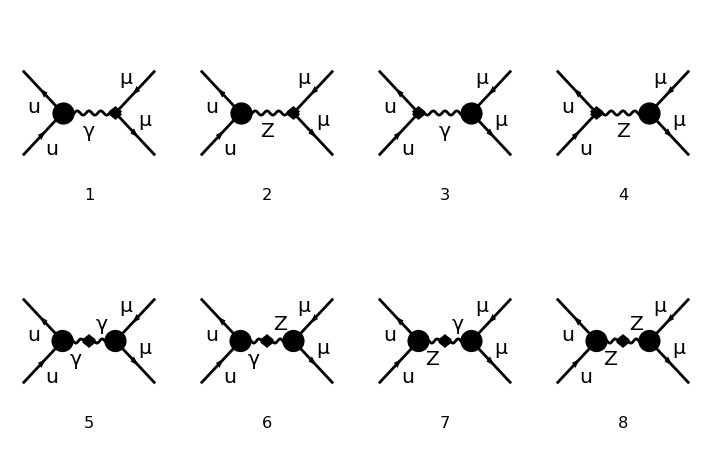

FeynArtsGraphics[][([1] | [2] | [3] | [4]
[5] | [6] | [7] | [8])]

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 2 Particles amplitudes

> Top. 3: 4 Particles amplitudes

in total: 8 Particles amplitudes

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-amp-1.frm

running FORM...

ok

```mathematica
tops1 = CreateCTTopologies[1, 2 -> 2,
  ExcludeTopologies -> {TadpoleCTs,WFCorrectionCTs (*loop counterterms*)}];
ins1 = InsertFields[tops1, process];
Paint[ins1,ColumnsXRows->{4,2},Numbering->Simple,
SheetHeader->None,ImageSize->{712,456}]
counter = CreateFeynAmp[ins1];
ct=CalcFeynAmp[counter];
counterterms = Unabbr[ct];
```

### Renormalization Constants (RC)

```mathematica
rc=CalcRenConst[counterterms];
ddd=Table[UVDivergentPart[rc[[1,i]]]//Simplify,{i,1,Length[rc[[1]]]}];
```

dMWsq1

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 6 Particles insertions

> Top. 2: 17 Particles insertions

Restoring 18 field point(s)

in total: 23 Particles insertions

creating amplitudes at level(s) {Particles}

> Top. 1: 6 Particles amplitudes

> Top. 2: 17 Particles amplitudes

in total: 23 Particles amplitudes

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-rc-1.frm

running FORM...

ok

dMZsq1

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 4 Particles insertions

> Top. 2: 20 Particles insertions

Restoring 18 field point(s)

in total: 24 Particles insertions

creating amplitudes at level(s) {Particles}

> Top. 1: 4 Particles amplitudes

> Top. 2: 20 Particles amplitudes

in total: 24 Particles amplitudes

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-rc-1.frm

running FORM...

ok

dSW1

dZAA1

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 2 Particles insertions

> Top. 2: 15 Particles insertions

Restoring 18 field point(s)

in total: 17 Particles insertions

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 15 Particles amplitudes

in total: 17 Particles amplitudes

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-rc-1.frm

running FORM...

ok

dZAZ1

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 2 Particles insertions

> Top. 2: 15 Particles insertions

Restoring 18 field point(s)

in total: 17 Particles insertions

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 15 Particles amplitudes

in total: 17 Particles amplitudes

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-rc-1.frm

running FORM...

ok

dZe1

dZZA1

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 2 Particles insertions

> Top. 2: 15 Particles insertions

Restoring 18 field point(s)

in total: 17 Particles insertions

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 15 Particles amplitudes

in total: 17 Particles amplitudes

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-rc-1.frm

running FORM...

ok

dZZZ1

dZfL1[2,2,2]

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 3 Particles insertions

Restoring 18 field point(s)

in total: 3 Particles insertions

creating amplitudes at level(s) {Particles}

> Top. 1: 3 Particles amplitudes

in total: 3 Particles amplitudes

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-rc-1.frm

running FORM...

ok

dZfL1[3,1,1]

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 3 Particles insertions

Restoring 18 field point(s)

in total: 3 Particles insertions

creating amplitudes at level(s) {Particles}

> Top. 1: 3 Particles amplitudes

in total: 3 Particles amplitudes

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-rc-1.frm

running FORM...

ok

dZfR1[2,2,2]

dZfR1[3,1,1]

## SELF+VERTICES->UV finite

## Vertici

```mathematica
ctvert=CCCCC*ExpandSums[counterterms[[1]]//.  {dMZsq1->0,dMWsq1->0,dSW1->0,dZAA1->0, dZZZ1->0, dZZA1->0, dZe1->0, dZAZ1->0}//.ddd];
```

```mathematica
uvvert1 = Collect[ provavert+ctvert, WeylChain[__], FullSimplify];
```

```mathematica
uvvert2= ExpandSums[ uvvert1 ] //.{CCCCC->1,VVVVV->1}//. MASSES //SMSimplify;
```

```mathematica
uvvert3= Collect[ uvvert2 , WeylChain[__], SMSimplify]
```

(2 Alfa2 Divergence (5 MZ2 SW2 Den[S,0]+(5 MW2-2 MZ2) Den[S,MZ2]) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3)))/(3 MZ2 SW2^2)+(4 Alfa2 Divergence (Den[S,0]-Den[S,MZ2]) Mat[SUNT[Col1,Col2]] ((v̇ 1|7|v3)) ((u̇ 4|6|u2)))/(3 SW2)+(2 Alfa2 Divergence (Den[S,0]-Den[S,MZ2]) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|v3)) ((u̇ 4|7|u2)))/SW2

## Self-energies

```mathematica
ctself=CCCCC*ExpandSums[counterterms[[1]]//.{dZfL1[__]->0,Conjugate[dZfL1[__]]->0,dZfR1[__]->0,Conjugate[dZfR1[__]]->0}//.ddd] ;
```

```mathematica
uvself1=Collect[ provaself+ctself, WeylChain[__], Simplify];
```

```mathematica
uvself2=ExpandSums[ uvself1 ] //.{CCCCC->1,SSSSS->1}//. MASSES   //SMFullSimplify;
```

```mathematica
uvself3=Collect[ uvself2, WeylChain[__], SMSimplify]
```

(2 Alfa2 Divergence (-5 MZ2 SW2 Den[S,0]+(-5 MW2+2 MZ2) Den[S,MZ2]) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3)))/(3 MZ2 SW2^2)-(4 Alfa2 Divergence (Den[S,0]-Den[S,MZ2]) Mat[SUNT[Col1,Col2]] ((v̇ 1|7|v3)) ((u̇ 4|6|u2)))/(3 SW2)-(2 Alfa2 Divergence (Den[S,0]-Den[S,MZ2]) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|v3)) ((u̇ 4|7|u2)))/SW2

## Vertici+Self

```mathematica
ct1=ExpandSums[counterterms[[1]]//.ddd] ;
```

```mathematica
c2=Collect[ provavert+provaself+ct1, WeylChain[__], Simplify];
```

```mathematica
c3=ExpandSums[ c2 ] //.{TTTTTT->1,SSSSS->1,VVVVV->1}/. MASSES   //SMSimplify
```

0